```mathematica
Notebook for the polynomial method in the Schroedinger equation. 
This example is for the case of the hexagonal well of side 1
```

Defining initialization variables

```mathematica
size=200;
L=1;
```

Symbolic integral of the generic x^n y^m integral term

```mathematica
$Assumptions={m≥0&&m∈Integers,n≥0&&n∈Integers,x∈Reals,y∈Reals};
integral[n_,m_]=(2^(-2-m-n) (1+(-1)^m) (1+(-1)^n))/((1+m) (1+n));
AbsoluteTiming[intTablehex=ParallelTable[integral[i,j],{i,0,200},{j,0,200},Method->"CoarsestGrained",DistributedContexts->Automatic];]
MyIntegral[n_,m_]:=MyIntegral[n,m]=intTablehex[[n+1,m+1]]
SetAttributes[MyIntegral,Listable]
AbsoluteTiming[ParallelTable[MyIntegral[i,j],{i,0,199},{j,0,199}];]
```

{4.66849,Null}

{0.692304,Null}

```mathematica
shape="square";
folder="~/agr_tese/data/symbolic_ortho/schrodinger/"<>shape<>"_";
basissize=ToString[Floor[size]];
CreateDirectory[folder<>basissize]//Quiet;
reg=Polygon[CirclePoints[L/√2,4]];
```

```mathematica
reg=Polygon[CirclePoints[L/√2,4]];
```

Defining normalization, scalar product, and Hamiltonian integration elements

```mathematica
coeffs[func_]:=coeffs[func]=GroebnerBasis`DistributedTermsList[func,{x,y},MonomialOrder->DegreeLexicographic][[1,All]]
SetAttributes[coeffs,Listable]

MyNorm[func1_]:=√MyProd2[func1]

mylist[func1_,func2_]:=coeffs[Flatten[Outer[Times,MonomialList[func1[x,y]],MonomialList[func2[x,y]]]]]

MyProd[f1_,f2_]:=Integrate[Expand[f1[x,y]*f2[x,y],Simplify],{x,y}∈reg]

MyProd2[func1_]:=Collect[Dot[(Flatten[(func1)[[All,All,2]]]),MyIntegral[(Flatten[(func1)[[All,All,1,1]]]),(Flatten[(func1)[[All,All,1,2]]])]],{x,y},Simplify]

Ham[f1_,f2_]:=(f1[x,y])*(D[f2[x,y],{x,2}]+D[f2[x,y],{y,2}])
En[func1_]:=-1*Inner[Times,(func1[[All,2]]),MyIntegral[func1[[All,1,1]],func1[[All,1,2]]],Plus]
```

Finding the numerical eigenvalues for comparison

```mathematica
exact=(1/π^2)*NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈reg,size];
```

Defining the basis functions. These are orthogonal by construction

```mathematica
poly[m_,n_,x_,y_]:=D[(x+L/2)^m(x-L/2)^m,{x,m}]*D[(y+L/2)^n(y-L/2)^n,{y,n}]

For[kk=1,kk<size+1,kk++,function[kk,x_,y_]=If[Mod[(kk-1)-(Floor[√(kk-1)])^2,2]==0,poly[Floor[√(kk-1)],((kk-1)-(Floor[√(kk-1)])^2)/2,x,y],poly[((kk-1)-(Floor[√(kk-1)])^2-1)/2,Floor[√(kk-1)],x,y]];]//AbsoluteTiming

fn[x_,y_]=(x^2-(L/2)^2)(y^2-(L/2)^2)/(√MyProd[(#1^2-(L/2)^2)(#2^2-(L/2)^2)&,(#1^2-(L/2)^2)(#2^2-(L/2)^2)&]);

ϕn[1,x_,y_]=function[1,x,y]*fn[x,y]/(√MyProd[function[1,#1,#2]*fn[#1,#2]&,function[1,#1,#2]*fn[#1,#2]&]);
```

{0.104419,Null}

```mathematica
ClearAll[Basis]
Basis[x_,y_]={ϕn[1,x,y]};
For[counter=2,counter<size+1,counter++,ϕun[counter,x_,y_]=Expand[function[counter,x,y]*fn[x,y],Simplify];
ϕu[counter,x_,y_]=Expand[ϕun[counter,x,y]-Dot[ParallelTable[MyProd2[mylist[ϕun[counter,#1,#2]&,ϕn[n,#1,#2]&]],{n,1,counter-1},Method->"CoarsestGrained"],Basis[x,y]]];
ϕn[counter,x_,y_]=Expand[ϕu[counter,x,y]/MyNorm[mylist[ϕu[counter,#1,#2]&,ϕu[counter,#1,#2]&]],Simplify];AppendTo[Basis[x,y],ϕn[counter,x,y]];
Print[counter]]//AbsoluteTiming
Length[Basis[x,y]]
```

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

{1043.23,Null}

200

Uncomment this table for verification of the orthogonality of the basis

```mathematica
(*ortho=ParallelTable[MyProd2[mylist[ϕn[b,#1,#2]&,ϕn[c,#1,#2]&]],{b,1,size},{c,1,b},Method->"FinestGrained",DistributedContexts->Automatic];//AbsoluteTiming
orthofull=MapThread[Join,{ortho,Rest/@Flatten[Conjugate[ortho],{{2},{1}}]}];
(orthofull//Chop)==IdentityMatrix[size]*)
```

Calculate the Hamiltonian matrix
It is Hermitian, so only the upper-triangular matrix is calculated

```mathematica
AbsoluteTiming[H=ParallelTable[Ham[ϕn[i,#1,#2]&,ϕn[j,#1,#2]&],{i,1,size},{j,1,i},Method->"FinestGrained",DistributedContexts->Automatic];]
AbsoluteTiming[Hn=ParallelTable[coeffs[H[[i,j]]],{i,1,size},{j,1,i},Method->"FinestGrained",DistributedContexts->Automatic];]
AbsoluteTiming[H2=ParallelTable[En[Hn[[i,j]]],{i,1,size},{j,1,i},Method->"FinestGrained",DistributedContexts->Automatic];]
AbsoluteTiming[Hfull=MapThread[Join,{H2,Rest/@Flatten[Conjugate[H2],{{2},{1}}]}];]
MatrixForm[Hfull]
```

{17.7657,Null}

{162.061,Null}

{116.08,Null}

{0.05948,Null}

(1)
 |  |  |  |

Obtaining the numerical eigenvalues and eigenvectors

```mathematica
$MaxExtraPrecision=10000;
eval=Eigenvalues[Chop[N[Hfull]]];//AbsoluteTiming
evec=Eigenvectors[Chop[N[Hfull]]];
```

{0.01234,Null}

```mathematica
eval[[;; -1]]
```

{31891.8,-15154.4,12561.1,12561.1,11993.5,11843.4,9745.82,9745.82,9732.62,9732.62,9701.41,9701.4,9452.04,8767.23,8757.32,8757.32,8679.25,8344.1,8166.55,8166.55,8046.5,8031.95,7923.82,7923.82,7835.42,7835.41,7767.16,7767.16,7766.32,7766.32,7716.98,7716.98,7687.37,7687.37,7628.78,7627.1,7032.95,7032.95,6821.47,6820.94,6750.43,6590.45,6590.45,6479.54,6479.21,6325.17,6325.17,6242.72,6242.72,6151.88,6151.88,6084.74,6084.74,4428.93,4195.04,4195.04,3262.46,3245.37,3205.99,3054.98,3054.98,2758.36,2745.74,2745.74,2630.82,2630.82,2598.9,2598.9,2554.52,2554.52,2456.64,2456.29,2438.86,2424.72,2314.42,2314.42,2285.63,2257.92,2257.92,2225.86,2225.86,2156.77,2156.77,2114.55,2114.36,2107.42,2107.42,2077.81,2077.81,1979.73,1979.73,1919.46,1919.46,1877.57,1877.57,1840.59,1787.18,1787.18,1719.59,1719.59,1683.58,1651.22,1526.36,1526.36,1458.64,1458.64,1401.5,1395.31,1330.1,1330.1,1309.63,1309.32,1298.71,1298.71,1286.06,1286.06,1278.1,1197.33,1197.33,1179.73,1179.73,1128.24,1128.24,1116.42,1116.42,1078.9,1078.9,1072.6,1072.6,1049.29,1049.29,988.426,987.764,983.396,983.396,967.584,914.667,914.667,879.176,879.176,841.8,841.8,839.073,839.073,811.811,811.811,790.359,790.359,730.552,730.551,721.271,721.271,710.615,671.923,671.923,642.315,642.315,641.722,641.722,602.046,602.046,572.638,572.638,523.097,523.097,513.22,513.22,493.485,493.485,493.48,444.133,444.133,404.654,404.654,394.785,394.785,365.176,365.176,335.567,335.567,315.827,286.219,286.219,256.61,256.61,246.74,246.74,197.392,197.392,177.653,167.783,167.783,128.305,128.305,98.696,98.696,78.9568,49.348,49.348,19.7392}

Plotting the eigenvalues

{2.,5.,5.,8.,10.,10.,13.,13.,17.,17.,18.,20.,20.,25.,25.,26.,26.,29.,29.,32.,34.,34.,37.0001,37.0001,40.0001,40.0001,41.,41.,45.0001,45.0001,50.,50.0005,50.0005,52.0001,52.0001,53.0008,53.0008,58.0204,58.0204,61.,61.,65.02,65.02,65.0801,65.0801,68.0801,68.0801,72.0004,73.0801,73.0801}

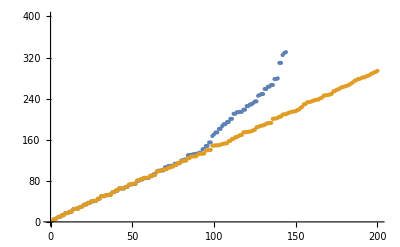

```mathematica
Sort[Abs[eval]/(π^2)][[;;50]]
ListPlot[{Sort[Abs[eval]/(π^2)],exact},PlotRange->{0,2*size}]
```

Defining the eigenbasis

```mathematica
Basis[x,y]=Table[function[i,x,y],{i,1,size}];
For[i=1,i<size+1,i++,
mode[i,x_,y_]=(evec[[i]]).Basis[x,y];
Print[i]]//AbsoluteTiming
BasisN[x_,y_]=Table[mode[aa,x,y],{aa,1,size}];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

{0.828611,Null}

Comparing eigenvalues

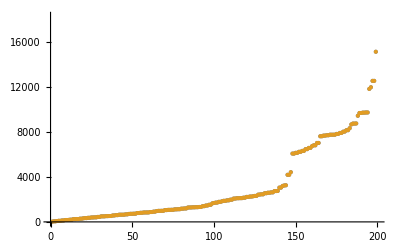

```mathematica
AAAA=Sort[Abs[Diagonal[(Conjugate[evec].Chop[N[Hfull]].Transpose[evec])]]];
ListPlot[{AAAA,Sort[Re[Abs[eval]]]}]
```

Exporting the data

```mathematica
Export[folder<>basissize<>"/eigenvalues.dat",Append[Sort[Re[Abs[eval]]],]]
Export[folder<>basissize<>"/basis.m",Basis[x,y]]
Export[folder<>basissize<>"/eigenvectors.m",evec]
Export[folder<>basissize<>"/full_hamiltonian.m",Hfull]
Export[folder<>basissize<>"/eigenfunctions.m",BasisN[x,y]]
```

~/agr_tese/data/symbolic_ortho/schrodinger/square_200/eigenvalues.dat

~/agr_tese/data/symbolic_ortho/schrodinger/square_200/basis.m

~/agr_tese/data/symbolic_ortho/schrodinger/square_200/eigenvectors.m

~/agr_tese/data/symbolic_ortho/schrodinger/square_200/full_hamiltonian.m

~/agr_tese/data/symbolic_ortho/schrodinger/square_200/eigenfunctions.m

Plotting the eigenfunctions

```mathematica
(*ParallelTable[{Plot3D[BasisN[x,y][[aa]],{x,y}∈reg,ImageSize->Large],DensityPlot[Abs[BasisN[x,y][[aa]]]^2,{x,y}∈reg,ImageSize->Large,ColorFunction->"SunsetColors",PlotPoints->100]},{aa,size,1,-1},Method->"CoarsestGrained",DistributedContexts->Automatic]//AbsoluteTiming*)
```

```mathematica
(*ParallelTable[Plot3D[ϕn[i,x,y],{x,y}∈reg,ColorFunction->"SunsetColors"],{i,1,size},Method->"FinestGrained"]*)
```